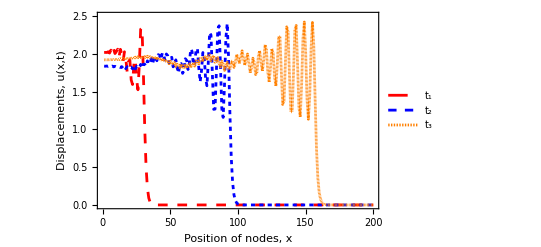

```mathematica
SetDirectory[NotebookDirectory[]];
mat2 = Import["Displacements_point3_4.txt","Table"];
For[i=1,i<201,i++,For[j=1,j<1001,j++,If[Abs[mat2[[i,j]]]<10^-4,mat2[[i,j]]=0,mat2[[i,j]]=mat2[[i,j]]]]]
plot=ListPlot[{-mat2[[All,100]],-mat2[[All,300]],-mat2[[All,500]]},PlotRange-> {0,2.5}, AspectRatio->1/GoldenRatio,Joined->True,FrameLabel-> {"Position of nodes, x","Displacements, u(x,t)"},Frame->True,PlotStyle->{{Directive[Red,AbsoluteThickness[2],AbsoluteDashing[7]]},{Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[3]]},{Directive[Orange],AbsoluteThickness[2],AbsoluteDashing[0]}},PlotLegends->LineLegend[Automatic,{"t_1","t_2","t_3"}],BaseStyle->{FontFamily->"Times",16}]
```

```mathematica
Export["precompressionWave.pdf",plot]
```

precompressionWave.pdf

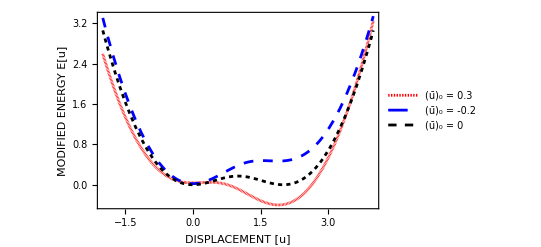

```mathematica
δ = 2;
l = 1;
k = 1;
u0 =0.3;
u1=-0.2;
L = √((δ/2)^2+l^2);
Lp[u_] := √(L^2- 2l u + u^2);
X[u_] := Lp[u]-L;
En[u_]:=k X[u]^2
F[u_] := -En'[u];
S[u_]:=En''[u];
energy=Plot[{En[u+u0]+F[u0]u,En[u+u1]+F[u1]u,En[u]},{u,-2l,4l},Frame->True, FrameLabel-> {"DISPLACEMENT [u]","MODIFIED ENERGY E[u]"},PlotStyle->{{Directive[Red,AbsoluteThickness[2],AbsoluteDashing[0]]},{Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[7]]},{Directive[Black,AbsoluteThickness[2],AbsoluteDashing[3]]}},PlotLegends->Placed[LineLegend[Automatic,{"(ū)_0 = 0.3","(ū)_0 = -0.2","(ū)_0 = 0"}],{Center,Top}]]
```

```mathematica
Export["precompressionEnergy.pdf",energy]
```

precompressionEnergy.pdf

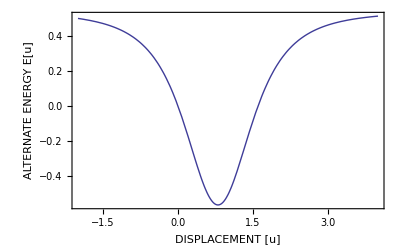

```mathematica
Plot[{En'[u+u0]+F[u0]-En'[u]},{u,-2l,4l},Frame->True, FrameLabel-> {"DISPLACEMENT [u]","ALTERNATE ENERGY E[u]"}]
```

```mathematica
plots=Table[ListPlot[-mat2[[All,2i]],Joined->True,PlotRange-> {0,2.5}],{i,1,400}];ListAnimate[plots]
```

```mathematica
Export["collision_animation.avi",plots]
```

collision_animation.avi

```mathematica
SetDirectory[NotebookDirectory[]];
mat2 = Import["Displacements_point03_4.txt","Table"];
For[i=1,i<201,i++,For[j=1,j<1001,j++,If[Abs[mat2[[i,j]]]<10^-4,mat2[[i,j]]=0,mat2[[i,j]]=mat2[[i,j]]]]]
mat3 = Table[-mat2[[All,i]],{i,1,800}];
image=ListContourPlot[mat3, FrameLabel->{"Position, x","Time, t"},PlotLegends->BarLegend[Automatic, LabelStyle->{FontSize->20}], BaseStyle->{FontFamily->"Times",20}]
```

```mathematica
image=-Graphics-
```

-Graphics-

```mathematica
Export["precompressioncontour.pdf",image]
```

precompressioncontour.pdf